## Importing eBird Data

```mathematica
byObservation=Import["/Users/katjad/Documents/eBird/Output/byCountry.json","RawJSON"];
byChecklist = Import["/Users/katjad/Documents/eBird/Output/byCountryByChecklist.json","RawJSON"];
byUser= Import["/Users/katjad/Documents/eBird/Output/byCountryByUser.json","RawJSON"];
```

```mathematica
byObservation[[1]]
```

<|1510012800→148,1510099200→160,1510185600→87,1510272000→53,1510358400→92,1541808000→25,1541894400→63,1541980800→65,1542067200→24,1542153600→13,1552521600→41,1552608000→64,1552694400→30,1556496000→114,1557187200→4,1573171200→15,1573344000→90,1573430400→19|>

## Converting into time series

#### US

```mathematica
USByObservation=TimeSeries[KeyMap[FromUnixTime[ToExpression[#]]&,byObservation["US"]]];
USByChecklist=TimeSeries[KeyMap[FromUnixTime[ToExpression[#]]&,byChecklist["US"]]];
USByUser=TimeSeries[KeyMap[FromUnixTime[ToExpression[#]]&,byUser["US"]]];
```

#### World

```mathematica
worldByObservation=TimeSeries[KeyMap[FromUnixTime[ToExpression[#]]&,Merge[Values[byObservation],Total]]];
worldByChecklist=TimeSeries[KeyMap[FromUnixTime[ToExpression[#]]&,Merge[Values[byChecklist],Total]]];
worldByUser=TimeSeries[KeyMap[FromUnixTime[ToExpression[#]]&,Merge[Values[byUser],Total]]];
```

## Plotting Time Series

### World

#### Absolute Numbers world

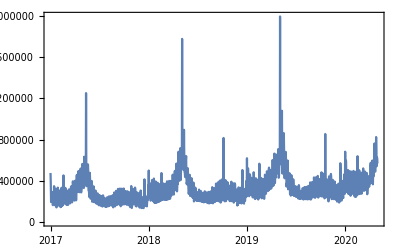

```mathematica
DateListPlot[worldByObservation,PlotRange->All]
```

#### Percentage Growth in Observations world

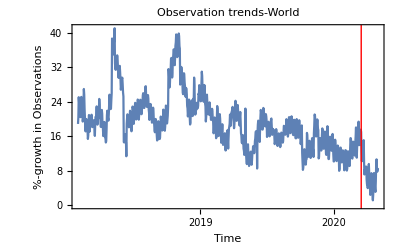

```mathematica
DateListPlot[MovingMap[(Last[#]-First[#])/First[#]*100&,MovingMap[Mean,worldByObservation,Quantity[1, "Months"]],Quantity[1, "Years"]],Epilog->{Red,InfiniteLine[{DateObject[{2020, 3, 15}],0},{0,1}]},Frame->True,FrameLabel->{"Time","%-growth in Observations"},PlotLabel->"Observation trends-World"]
```

#### Percentage Growth in Checklists world

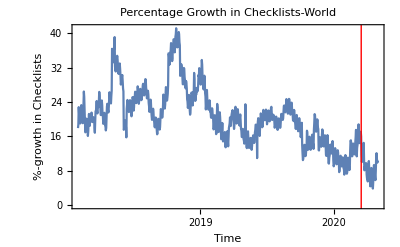

```mathematica
DateListPlot[MovingMap[(Last[#]-First[#])/First[#]*100&,MovingMap[Mean,worldByChecklist,Quantity[1, "Months"]],Quantity[1, "Years"]],Epilog->{Red,InfiniteLine[{DateObject[{2020, 3, 15}],0},{0,1}]},Frame->True,FrameLabel->{"Time","%-growth in Checklists"},PlotLabel->"Percentage Growth in Checklists-World"]
```

#### Percentage growth in Users

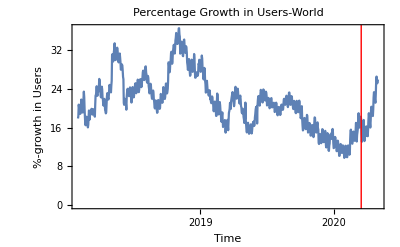

```mathematica
DateListPlot[MovingMap[(Last[#]-First[#])/First[#]*100&,MovingMap[Mean,worldByUser,LinguisticAssistant],Quantity[1, "Years"]],Epilog->{Red,InfiniteLine[{DateObject[{2020, 3, 15}],0},{0,1}]},Frame->True,FrameLabel->{"Time","%-growth in Users"},PlotLabel->"Percentage Growth in Users-World"]
```

### United States

#### Percentage growth in observations US

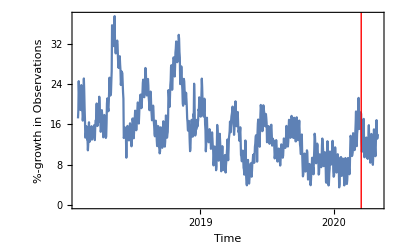

```mathematica
DateListPlot[MovingMap[(Last[#]-First[#])/First[#]*100&,MovingMap[Mean,USByObservation,Quantity[1, "Months"]],Quantity[1, "Years"]],Epilog->{Red,InfiniteLine[{DateObject[{2020, 3, 15}],0},{0,1}]},Frame->True,FrameLabel->{"Time","%-growth in Observations"}]
```